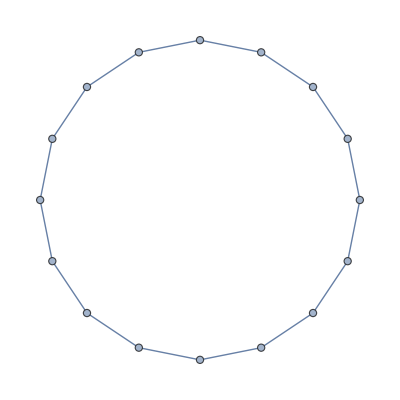
```mathematica
c16=CycleGraph[16];

assoc=FindSubgraphIsomorphism[c16,gl[[6]],2][[1]]
(*reverseAssoc=Association@KeyValueMap[#2->#1&,assoc];
g=Graph[EdgeList[gl[[6]]]/.reverseAssoc]*)
FindIsomorphicSubgraph[g,c16]
pm=PermutationMatrix[{1,2,3,13,14,10,4,16,17,9,8,7,6,5,15,11,12}]
ipm=pm+(IdentityMatrix[Dimensions[pm][[1]]]-DiagonalMatrix[Diagonal[pm]])
MatrixForm@ipm
m=AdjacencyMatrix[gl[[6]]].ipm
MatrixForm[m]
AdjacencyGraph[m]
(*FindHamiltonianCycle[VertexDelete[g,{1}],2]
HighlightGraph[VertexDelete[g,{1}],VertexShapeFunction->"Name"]*)

<|1->1,2->2,3->3,4->7,5->17,6->16,7->15,8->14,9->13,10->12,11->11,12->10,13->9,14->8,15->4,16->5|>
{-Graphics-}
PermutationMatrix[…]
{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1}}
({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 1}})
{{0,1,1,1,1,0,0,0,0,0,0,0,1,1,0,0,0},{1,0,0,1,0,1,1,1,1,1,0,0,0,0,0,1,1},{1,0,0,0,0,0,1,1,2,1,1,1,0,0,0,0,1},{1,0,0,0,1,1,1,0,0,0,0,1,1,1,1,0,0},{1,0,0,0,0,0,0,1,0,0,1,1,0,0,1,2,1},{0,1,0,0,0,1,1,0,1,1,1,1,1,0,0,1,0},{0,1,0,0,1,0,1,1,0,0,1,2,0,1,0,0,1},{0,1,0,0,2,1,1,0,0,0,0,1,1,2,0,0,0},{0,1,1,0,0,0,0,0,0,0,1,1,0,0,1,1,1},{0,0,1,0,1,1,0,0,0,1,0,1,0,1,1,0,1},{0,0,1,1,0,1,1,0,0,0,1,0,1,0,1,1,0},{0,0,1,2,0,1,1,1,0,1,0,0,1,0,0,1,0},{0,0,0,1,0,1,0,2,0,1,1,1,1,0,0,1,1},{0,0,0,2,0,0,1,1,1,1,1,0,1,0,0,2,0},{0,0,0,1,1,0,0,1,2,1,1,0,1,1,0,0,1},{0,0,0,0,2,1,0,1,1,1,1,0,0,2,0,0,1},{0,0,0,1,1,1,1,0,2,1,0,0,1,1,0,0,1}}
({{0, 1, 1, 1, 1, 0, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0}, {1, 0, 0, 1, 0, 1, 1, 1, 1, 1, 0, 0, 0, 0, 0, 1, 1}, {1, 0, 0, 0, 0, 0, 1, 1, 2, 1, 1, 1, 0, 0, 0, 0, 1}, {1, 0, 0, 0, 1, 1, 1, 0, 0, 0, 0, 1, 1, 1, 1, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 1, 0, 0, 1, 1, 0, 0, 1, 2, 1}, {0, 1, 0, 0, 0, 1, 1, 0, 1, 1, 1, 1, 1, 0, 0, 1, 0}, {0, 1, 0, 0, 1, 0, 1, 1, 0, 0, 1, 2, 0, 1, 0, 0, 1}, {0, 1, 0, 0, 2, 1, 1, 0, 0, 0, 0, 1, 1, 2, 0, 0, 0}, {0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 1, 1, 1}, {0, 0, 1, 0, 1, 1, 0, 0, 0, 1, 0, 1, 0, 1, 1, 0, 1}, {0, 0, 1, 1, 0, 1, 1, 0, 0, 0, 1, 0, 1, 0, 1, 1, 0}, {0, 0, 1, 2, 0, 1, 1, 1, 0, 1, 0, 0, 1, 0, 0, 1, 0}, {0, 0, 0, 1, 0, 1, 0, 2, 0, 1, 1, 1, 1, 0, 0, 1, 1}, {0, 0, 0, 2, 0, 0, 1, 1, 1, 1, 1, 0, 1, 0, 0, 2, 0}, {0, 0, 0, 1, 1, 0, 0, 1, 2, 1, 1, 0, 1, 1, 0, 0, 1}, {0, 0, 0, 0, 2, 1, 0, 1, 1, 1, 1, 0, 0, 2, 0, 0, 1}, {0, 0, 0, 1, 1, 1, 1, 0, 2, 1, 0, 0, 1, 1, 0, 0, 1}})
-Graphics-
```

```mathematica
m=AdjacencyMatrix[gl[[6]]]
pm=Transpose[m[[{1,2,3,13,14,10,4,16,17,9,8,7,6,5,15,11,12}]]][[{1,2,3,13,14,10,4,16,17,9,8,7,6,5,15,11,12}]]
```